```mathematica
ClearAll["Global`*"]
```

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
(*1D Bloch periodic Hamiltonian with Periodic BC*)
```

```mathematica
L=5;
a=-L/2;
A[t_]:=Sin[t]
V3[x_,t_]:=3+A[t]*Cos[2*Pi*1*x/L]
λ=Pi/2;
Ntot=4;
i=3;
k=((2*i-Ntot-1)/(2*Ntot))*2*Pi/L (*wave #*)
```

π/20

```mathematica
vals3=NDEigenvalues[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V3[x,λ]*u[x],u[a]==u[a+L]},u[x],{x,a,a+L},6]
```

{2.73742-4.26034×10^-15 ⅈ,4.30076-1.24986×10^-14 ⅈ,5.08774+2.04599×10^-16 ⅈ,8.57739-1.09339×10^-14 ⅈ,10.1508+1.41334×10^-15 ⅈ,16.0774+3.90077×10^-15 ⅈ}

```mathematica
ufun31=NDSolve[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V3[x,λ]*u[x]==vals3[[1]]*u[x],u[a]==u[a+L],u[a]==0.23327569085619906},u[x],{x,a,a+L}]
(*Case Bloch Hailtonain(denoted by 3), λ=Pi/2 and 1st eigen value (denoted 1)*)
vals3[[1]]
```

{{u[x]→InterpolatingFunction[…][x]}}

2.73742-4.26034×10^-15 ⅈ

```mathematica
v1[x_]:=Evaluate[u[x]/.ufun31]/Sqrt[NIntegrate[Abs[Evaluate[u[x]/.ufun31]]^2,{x,a,a+L}]];(*checking normalization*)
NIntegrate[Abs[v1[x]]^2,{x,a,a+L}]
```

{1.}

```mathematica
ufun32=NDSolve[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V3[x,λ]*u[x]==vals3[[2]]*u[x],u[a]==u[a+L],u[a]==0.310451910408699},u[x],{x,a,a+L}](*Case Bloch Hailtonain(denoted by 3), λ=Pi/2 and 2nd eigen value (denoted 2)*)
vals3[[2]]
```

{{u[x]→InterpolatingFunction[…][x]}}

4.30076-1.24986×10^-14 ⅈ

```mathematica
v2[x_]:=Evaluate[u[x]/.ufun32]/Sqrt[NIntegrate[Abs[Evaluate[u[x]/.ufun32]]^2,{x,a,a+L}]];
NIntegrate[Abs[v2[x]]^2,{x,a,a+L}](*checking normalization*)
```

{1.}

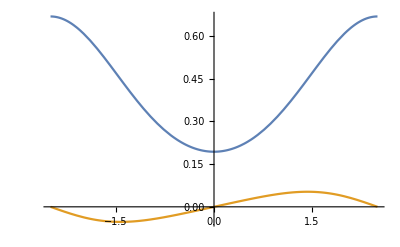

```mathematica
Plot[{Evaluate[Re[v1[x]]],Evaluate[Im[v1[x]]]},{x,a,a+L},PlotRange->Full](*real and complex part of ufun31*)
```

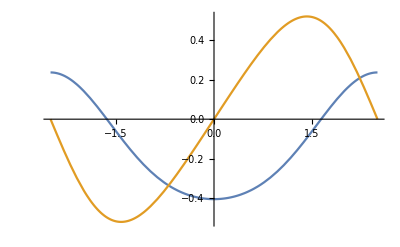

```mathematica
Plot[{Evaluate[Re[v2[x]]],Evaluate[Im[v2[x]]]},{x,a,a+L},PlotRange->Full](*real and complex part of ufun32*)
```

```mathematica
NIntegrate[Conjugate[v2[x]]*v1[x]*x,{x,a,a+L}] (*LHS of eqn. 4.15 for (a,a+L]*)
```

{5.57699×10^-7-1.04147 ⅈ}

```mathematica
myperiodic[func_,{val_Symbol,min_?NumericQ,max_?NumericQ}]:=func/. (val:>Mod[val-min,max-min]+min)
```

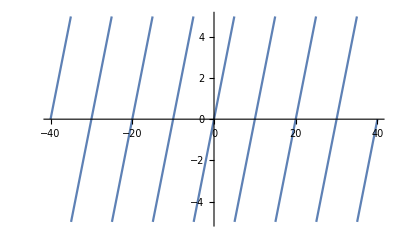

```mathematica
Plot[myperiodic[t, {t, -5, 5}] // Evaluate, {t, -40, 40}](*Testing out my periodic*)
```

```mathematica
g1[x_]:=myperiodic[v1[x], {x, a, a+L}](*periodicaly extending fn case 31, ie, v1*)
```

```mathematica
g2[x_]:=myperiodic[v2[x], {x, a, a+L}](*periodicaly extending the fn case 32, ie, v2*)
```

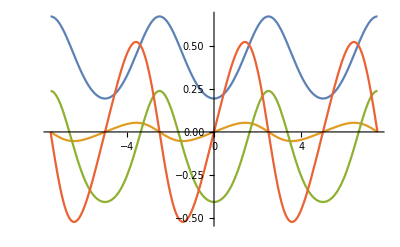

```mathematica
Plot[{Re[g1[x]],Im[g1[x]],Re[g2[x]],Im[g2[x]]}// Evaluate, {x, a-L, a+2*L}]
```

```mathematica
(*Plot[{Re[g1[x]],Im[g1[x]]}// Evaluate, {x, a-L, a+2*L}]*)
```

```mathematica
(*Plot[{Re[g2[x]],Im[g2[x]]}// Evaluate, {x, a-L, a+2*L}]*)
```

```mathematica
(*Manipulate[NIntegrate[Conjugate[g2[x]]*g1[x]*x,{x,b,b+L}],{b,a-L,a+2*L}](*LHS of eqn. 4.15 for arbit unit cell (b,b+L]*)(*Computationally Expensive*)*)(*Manipulate[NIntegrate[Conjugate[g2[x]]*D[g1[x],x]/(vals3[[1]]-vals3[[2]]),{x,b,b+L}],{b,a-L,a+2*L}](*RHS of eqn. 4.15 for arbit unit cell (b,b+L]*)*)(*Computationally expensice*)
```

```mathematica
DataLHS={};
DataRHS={};
For[b=a,b≤a+L,b=b+L/60,LH=NIntegrate[Conjugate[g2[x]]*g1[x]*x,{x,b,b+L}];AppendTo[DataLHS,{b,LH}]]
For[b=a,b≤a+L,b=b+L/60,RH=NIntegrate[Conjugate[g2[x]]*D[g1[x],x]/(vals3[[1]]-vals3[[2]]),{x,b,b+L}];AppendTo[DataRHS,{b,RH}]]
DataLHS
DataRHS
```

{{-5/2,{5.57699×10^-7-1.04147 ⅈ}},{-29/12,{0.0659056-1.03258 ⅈ}},{-7/3,{0.13033-1.0062 ⅈ}},{-9/4,{0.191855-0.963141 ⅈ}},{-13/6,{0.249187-0.904722 ⅈ}},{-25/12,{0.301202-0.83268 ⅈ}},{-2,{0.346995-0.749082 ⅈ}},{-23/12,{0.385893-0.656217 ⅈ}},{-11/6,{0.417476-0.556486 ⅈ}},{-7/4,{0.441565-0.452298 ⅈ}},{-5/3,{0.458208-0.345963 ⅈ}},{-19/12,{0.467656-0.239621 ⅈ}},{-3/2,{0.470323-0.13517 ⅈ}},{-17/12,{0.46675-0.0342286 ⅈ}},{-4/3,{0.457569+0.0618886 ⅈ}},{-5/4,{0.443459+0.152172 ⅈ}},{-7/6,{0.425114+0.235908 ⅈ}},{-13/12,{0.403217+0.312648 ⅈ}},{-1,{0.37841+0.382182 ⅈ}},{-11/12,{0.351283+0.444493 ⅈ}},{-5/6,{0.322358+0.49972 ⅈ}},{-3/4,{0.292086+0.548118 ⅈ}},{-2/3,{0.260842+0.590017 ⅈ}},{-7/12,{0.228931+0.625791 ⅈ}},{-1/2,{0.19659+0.65583 ⅈ}},{-5/12,{0.163995+0.680511 ⅈ}},{-1/3,{0.131269+0.700183 ⅈ}},{-1/4,{0.0984914+0.71515 ⅈ}},{-1/6,{0.0657055+0.725658 ⅈ}},{-1/12,{0.0329289+0.731889 ⅈ}},{0,{0.000161212+0.733953 ⅈ}},{1/12,{-0.0326065+0.731889 ⅈ}},{1/6,{-0.0653831+0.725658 ⅈ}},{1/4,{-0.0981689+0.71515 ⅈ}},{1/3,{-0.130947+0.700183 ⅈ}},{5/12,{-0.163673+0.680511 ⅈ}},{1/2,{-0.196268+0.65583 ⅈ}},{7/12,{-0.228609+0.625791 ⅈ}},{2/3,{-0.26052+0.590016 ⅈ}},{3/4,{-0.291763+0.548118 ⅈ}},{5/6,{-0.322036+0.49972 ⅈ}},{11/12,{-0.350961+0.444493 ⅈ}},{1,{-0.378088+0.382182 ⅈ}},{13/12,{-0.402894+0.312648 ⅈ}},{7/6,{-0.424792+0.235908 ⅈ}},{5/4,{-0.443136+0.152172 ⅈ}},{4/3,{-0.457246+0.0618885 ⅈ}},{17/12,{-0.466427-0.0342286 ⅈ}},{3/2,{-0.469999-0.13517 ⅈ}},{19/12,{-0.467333-0.239621 ⅈ}},{5/3,{-0.457885-0.345963 ⅈ}},{7/4,{-0.441241-0.452298 ⅈ}},{11/6,{-0.417152-0.556486 ⅈ}},{23/12,{-0.385569-0.656216 ⅈ}},{2,{-0.346671-0.749081 ⅈ}},{25/12,{-0.300878-0.83268 ⅈ}},{13/6,{-0.248862-0.904722 ⅈ}},{9/4,{-0.191531-0.963141 ⅈ}},{7/3,{-0.130006-1.0062 ⅈ}},{29/12,{-0.0655813-1.03258 ⅈ}},{5/2,{0.000323749-1.04147 ⅈ}}}

{{-5/2,{-1.58507×10^-7+0.282253 ⅈ}},{-29/12,{-1.58507×10^-7+0.282253 ⅈ}},{-7/3,{-1.58507×10^-7+0.282253 ⅈ}},{-9/4,{-1.58507×10^-7+0.282253 ⅈ}},{-13/6,{-1.58507×10^-7+0.282253 ⅈ}},{-25/12,{-1.58507×10^-7+0.282253 ⅈ}},{-2,{-1.58507×10^-7+0.282253 ⅈ}},{-23/12,{-1.58507×10^-7+0.282253 ⅈ}},{-11/6,{-1.58507×10^-7+0.282253 ⅈ}},{-7/4,{-1.58507×10^-7+0.282253 ⅈ}},{-5/3,{-1.58507×10^-7+0.282253 ⅈ}},{-19/12,{-1.58507×10^-7+0.282253 ⅈ}},{-3/2,{-1.58507×10^-7+0.282253 ⅈ}},{-17/12,{-1.58507×10^-7+0.282253 ⅈ}},{-4/3,{-1.58507×10^-7+0.282253 ⅈ}},{-5/4,{-1.58507×10^-7+0.282253 ⅈ}},{-7/6,{-1.58507×10^-7+0.282253 ⅈ}},{-13/12,{-1.58507×10^-7+0.282253 ⅈ}},{-1,{-1.58507×10^-7+0.282253 ⅈ}},{-11/12,{-1.58507×10^-7+0.282253 ⅈ}},{-5/6,{-1.58507×10^-7+0.282253 ⅈ}},{-3/4,{-1.58507×10^-7+0.282253 ⅈ}},{-2/3,{-1.58507×10^-7+0.282253 ⅈ}},{-7/12,{-1.58507×10^-7+0.282253 ⅈ}},{-1/2,{-1.58507×10^-7+0.282253 ⅈ}},{-5/12,{-1.58507×10^-7+0.282253 ⅈ}},{-1/3,{-1.58507×10^-7+0.282253 ⅈ}},{-1/4,{-1.58507×10^-7+0.282253 ⅈ}},{-1/6,{-1.58507×10^-7+0.282253 ⅈ}},{-1/12,{-1.58507×10^-7+0.282253 ⅈ}},{0,{-1.58507×10^-7+0.282253 ⅈ}},{1/12,{-1.58507×10^-7+0.282253 ⅈ}},{1/6,{-1.58507×10^-7+0.282253 ⅈ}},{1/4,{-1.58507×10^-7+0.282253 ⅈ}},{1/3,{-1.58507×10^-7+0.282253 ⅈ}},{5/12,{-1.58507×10^-7+0.282253 ⅈ}},{1/2,{-1.58507×10^-7+0.282253 ⅈ}},{7/12,{-1.58507×10^-7+0.282253 ⅈ}},{2/3,{-1.58507×10^-7+0.282253 ⅈ}},{3/4,{-1.58507×10^-7+0.282253 ⅈ}},{5/6,{-1.58507×10^-7+0.282253 ⅈ}},{11/12,{-1.58507×10^-7+0.282253 ⅈ}},{1,{-1.58507×10^-7+0.282253 ⅈ}},{13/12,{-1.58507×10^-7+0.282253 ⅈ}},{7/6,{-1.58507×10^-7+0.282253 ⅈ}},{5/4,{-1.58507×10^-7+0.282253 ⅈ}},{4/3,{-1.58507×10^-7+0.282253 ⅈ}},{17/12,{-1.58507×10^-7+0.282253 ⅈ}},{3/2,{-1.58507×10^-7+0.282253 ⅈ}},{19/12,{-1.58507×10^-7+0.282253 ⅈ}},{5/3,{-1.58507×10^-7+0.282253 ⅈ}},{7/4,{-1.58507×10^-7+0.282253 ⅈ}},{11/6,{-1.58507×10^-7+0.282253 ⅈ}},{23/12,{-1.58507×10^-7+0.282253 ⅈ}},{2,{-1.58507×10^-7+0.282253 ⅈ}},{25/12,{-1.58507×10^-7+0.282253 ⅈ}},{13/6,{-1.58507×10^-7+0.282253 ⅈ}},{9/4,{-1.58507×10^-7+0.282253 ⅈ}},{7/3,{-1.58507×10^-7+0.282253 ⅈ}},{29/12,{-1.58507×10^-7+0.282253 ⅈ}},{5/2,{-1.58507×10^-7+0.282253 ⅈ}}}

-Graphics-

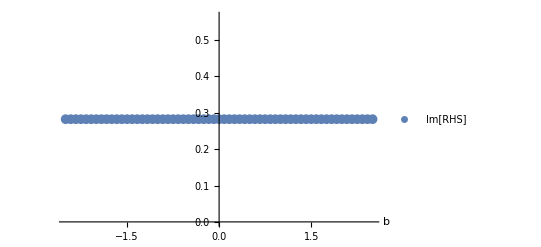

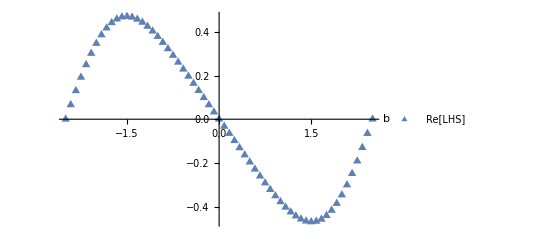

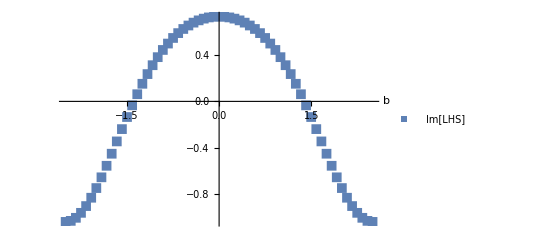

```mathematica
Data1RHSRe=Range[Length[DataRHS]];
Data1RHSIm=Range[Length[DataRHS]];
Data2LHSRe=Range[Length[DataLHS]];
Data2LHSIm=Range[Length[DataLHS]];
For[i=1,i≤Length[DataRHS],i=i+1,Data1RHSRe[[i]]={DataRHS[[i]][[1]],Re[DataRHS[[i]][[2]][[1]]]}]
For[i=1,i≤Length[DataRHS],i=i+1,Data1RHSIm[[i]]={DataRHS[[i]][[1]],Im[DataRHS[[i]][[2]][[1]]]}]
For[i=1,i≤Length[DataLHS],i=i+1,Data2LHSRe[[i]]={DataLHS[[i]][[1]],Re[DataLHS[[i]][[2]][[1]]]}]
For[i=1,i≤Length[DataLHS],i=i+1,Data2LHSIm[[i]]={DataLHS[[i]][[1]],Im[DataLHS[[i]][[2]][[1]]]}]
p1=ListPlot[Data1RHSRe,PlotMarkers->"*",AxesLabel->{"b"," "},PlotLegends->{"Re[RHS]"}]
p2=ListPlot[Data1RHSIm,PlotMarkers->{●,10},AxesLabel->{"b"," "},PlotLegends->{"Im[RHS]"}]
p3=ListPlot[Data2LHSRe,PlotMarkers->{▲,10},AxesLabel->{"b"," "},PlotLegends->{"Re[LHS]"}]
p4=ListPlot[Data2LHSIm,PlotMarkers->{■,10},AxesLabel->{"b"," "},PlotLegends->{"Im[LHS]"}]
```

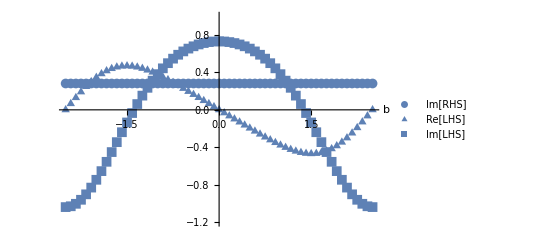

-Graphics-

```mathematica
Show[p2,p3,p4,PlotRange->{{a,a+L},{-1.2,1}},LabelStyle->{FontSize->12,FontFamily->"Times", ,Black,Bold},AxesStyle->{Arrowheads[{0.0,0.02}]}]
```

```mathematica
(*Note that the RHS is independent of choice of b, while the LHS isn't.*)
```